```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY190/sec_int_data/862nm.dat"]
```

{{1.16196,-0.144991},{1.1485,-0.164097},{1.13288,-0.171488},{1.11879,-0.309273},{1.10986,-0.581391},{1.10188,-0.881117},{1.0953,-1.18277},{1.09118,-1.25906},{1.08898,-0.938664},{1.08844,-0.485515},{1.08969,-0.332596},{1.094,-0.19911},{1.09832,-0.167461},{1.10319,-0.137218},{1.11502,-0.141126},{1.13408,-0.122303},{1.14571,-0.113919},{1.16039,-0.117894},{1.17699,-0.130576},{1.19764,-0.109302},{1.21871,-0.135923},{1.24216,-0.122586},{1.26543,-0.122473},{1.29691,-0.106995},{1.32536,-0.117804},{1.37118,-0.12655},{1.45421,-0.174008}}

-2.13639+1.55205 x

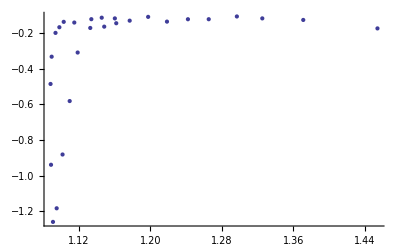

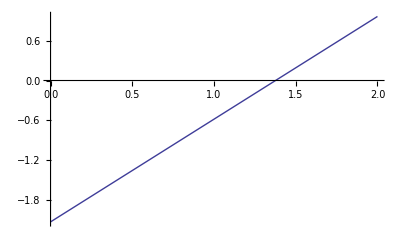

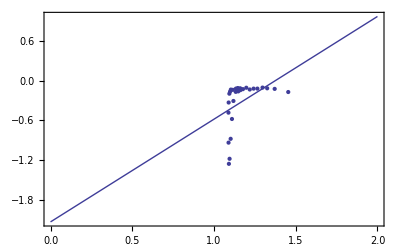

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```